```mathematica
(*Mathematica*)
```

```mathematica
(* Riemannian three attractor model {0,1,Infinity} on Poincare disk with Cauchy wave function: long tailed distribution*)
```

```mathematica
(*Cauchy wave function*)
```

```mathematica
Clear[Ψ,Ψ0,r]
```

```mathematica
Ψ[r_]=Ψ0/(1+r^2)
```

Ψ0/(1+r^2)

```mathematica
(*Normalization*)
```

```mathematica
w=Integrate[Ψ[r],{r,0,Infinity}]
```

(π Ψ0)/2

```mathematica
Ψ0=2/Pi
```

2/π

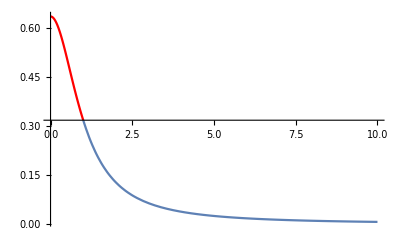

```mathematica
g0=Show[{Plot[Ψ[r],{r,0,1},PlotStyle->Red,PlotRange->All],Plot[Ψ[r],{r,1,10},PlotRange->All]},PlotRange->All]
```

```mathematica
Integrate[Ψ[r],{r,0,r0}]+Integrate[Ψ[r],{r,r0,Infinity}]
```

ConditionalExpression[1, -1<Im[r0]<0||0<Im[r0]<1||Re[r0]≠0]

```mathematica
(*https://en.wikipedia.org/wiki/Schr%C3%B6dinger_equation*)
```

```mathematica
(*quantum Poincare-Cauchy gravity to mass*)
```

```mathematica
(*Gravitaional Potental*)
```

```mathematica
Clear[m]
```

```mathematica
V=4*Pi*G*m^2/r
```

(4 G m^2 π)/r

```mathematica
E0=ExpandAll[(1+r^2)^3*((-hbar^2/(2*m))*D[Ψ[r],{r,2}]+V*Ψ[r]-i*hbar*Exp[I*2*m*c^2/hbar]*Ψ[r])]
```

-(2 ⅇ^((2 ⅈ c^2 m)/hbar) hbar i)/(π+π r^2)-(6 ⅇ^((2 ⅈ c^2 m)/hbar) hbar i r^2)/(π+π r^2)-(6 ⅇ^((2 ⅈ c^2 m)/hbar) hbar i r^4)/(π+π r^2)-(2 ⅇ^((2 ⅈ c^2 m)/hbar) hbar i r^6)/(π+π r^2)+(8 G m^2)/(r+r^3)+(24 G m^2 r^2)/(r+r^3)+(24 G m^2 r^4)/(r+r^3)+(8 G m^2 r^6)/(r+r^3)+(2 hbar^2)/(m π (1+2 r^2+r^4))+(6 hbar^2 r^2)/(m π (1+2 r^2+r^4))+(6 hbar^2 r^4)/(m π (1+2 r^2+r^4))+(2 hbar^2 r^6)/(m π (1+2 r^2+r^4))-(8 hbar^2 r^2)/(m π (1+3 r^2+3 r^4+r^6))-(24 hbar^2 r^4)/(m π (1+3 r^2+3 r^4+r^6))-(24 hbar^2 r^6)/(m π (1+3 r^2+3 r^4+r^6))-(8 hbar^2 r^8)/(m π (1+3 r^2+3 r^4+r^6))

```mathematica
Reduce[E0==0,{m,r}]
```

(G m≠0&&hbar==0&&(r==-ⅈ||r==ⅈ))||(hbar i m≠0&&r≠0&&(r==Root[-4 G m^3 π+(-hbar^2+ⅇ^((2 ⅈ c^2 m)/hbar) hbar i m) #1-8 G m^3 π #1^2+(3 hbar^2+2 ⅇ^((2 ⅈ c^2 m)/hbar) hbar i m) #1^3-4 G m^3 π #1^4+ⅇ^((2 ⅈ c^2 m)/hbar) hbar i m #1^5&,1]||r==Root[-4 G m^3 π+(-hbar^2+ⅇ^((2 ⅈ c^2 m)/hbar) hbar i m) #1-8 G m^3 π #1^2+(3 hbar^2+2 ⅇ^((2 ⅈ c^2 m)/hbar) hbar i m) #1^3-4 G m^3 π #1^4+ⅇ^((2 ⅈ c^2 m)/hbar) hbar i m #1^5&,2]||r==Root[-4 G m^3 π+(-hbar^2+ⅇ^((2 ⅈ c^2 m)/hbar) hbar i m) #1-8 G m^3 π #1^2+(3 hbar^2+2 ⅇ^((2 ⅈ c^2 m)/hbar) hbar i m) #1^3-4 G m^3 π #1^4+ⅇ^((2 ⅈ c^2 m)/hbar) hbar i m #1^5&,3]||r==Root[-4 G m^3 π+(-hbar^2+ⅇ^((2 ⅈ c^2 m)/hbar) hbar i m) #1-8 G m^3 π #1^2+(3 hbar^2+2 ⅇ^((2 ⅈ c^2 m)/hbar) hbar i m) #1^3-4 G m^3 π #1^4+ⅇ^((2 ⅈ c^2 m)/hbar) hbar i m #1^5&,4]||r==Root[-4 G m^3 π+(-hbar^2+ⅇ^((2 ⅈ c^2 m)/hbar) hbar i m) #1-8 G m^3 π #1^2+(3 hbar^2+2 ⅇ^((2 ⅈ c^2 m)/hbar) hbar i m) #1^3-4 G m^3 π #1^4+ⅇ^((2 ⅈ c^2 m)/hbar) hbar i m #1^5&,5]))||(m r≠0&&G==0&&hbar==0)||(hbar≠0&&G m≠0&&i==0&&(r==Root[4 G m^3 π+hbar^2 #1+8 G m^3 π #1^2-3 hbar^2 #1^3+4 G m^3 π #1^4&,1]||r==Root[4 G m^3 π+hbar^2 #1+8 G m^3 π #1^2-3 hbar^2 #1^3+4 G m^3 π #1^4&,2]||r==Root[4 G m^3 π+hbar^2 #1+8 G m^3 π #1^2-3 hbar^2 #1^3+4 G m^3 π #1^4&,3]||r==Root[4 G m^3 π+hbar^2 #1+8 G m^3 π #1^2-3 hbar^2 #1^3+4 G m^3 π #1^4&,4]))||(hbar m≠0&&G==0&&i==0&&(r==-1/(√3)||r==1/(√3)))

```mathematica
s1=r/.Solve[E0==0,{m,r}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

Solve::svars: Equations may not give solutions for all "solve" variables.

{Root[(4 c^6 G m^3 π)/hbar^2+(c^6-(c^6 ⅇ^((2 ⅈ c^2 m)/hbar) i m)/hbar) #1+(8 c^6 G m^3 π #1^2)/hbar^2+(-3 c^6-(2 c^6 ⅇ^((2 ⅈ c^2 m)/hbar) i m)/hbar) #1^3+(4 c^6 G m^3 π #1^4)/hbar^2-(c^6 ⅇ^((2 ⅈ c^2 m)/hbar) i m #1^5)/hbar&,1],Root[(4 c^6 G m^3 π)/hbar^2+(c^6-(c^6 ⅇ^((2 ⅈ c^2 m)/hbar) i m)/hbar) #1+(8 c^6 G m^3 π #1^2)/hbar^2+(-3 c^6-(2 c^6 ⅇ^((2 ⅈ c^2 m)/hbar) i m)/hbar) #1^3+(4 c^6 G m^3 π #1^4)/hbar^2-(c^6 ⅇ^((2 ⅈ c^2 m)/hbar) i m #1^5)/hbar&,2],Root[(4 c^6 G m^3 π)/hbar^2+(c^6-(c^6 ⅇ^((2 ⅈ c^2 m)/hbar) i m)/hbar) #1+(8 c^6 G m^3 π #1^2)/hbar^2+(-3 c^6-(2 c^6 ⅇ^((2 ⅈ c^2 m)/hbar) i m)/hbar) #1^3+(4 c^6 G m^3 π #1^4)/hbar^2-(c^6 ⅇ^((2 ⅈ c^2 m)/hbar) i m #1^5)/hbar&,3],Root[(4 c^6 G m^3 π)/hbar^2+(c^6-(c^6 ⅇ^((2 ⅈ c^2 m)/hbar) i m)/hbar) #1+(8 c^6 G m^3 π #1^2)/hbar^2+(-3 c^6-(2 c^6 ⅇ^((2 ⅈ c^2 m)/hbar) i m)/hbar) #1^3+(4 c^6 G m^3 π #1^4)/hbar^2-(c^6 ⅇ^((2 ⅈ c^2 m)/hbar) i m #1^5)/hbar&,4],Root[(4 c^6 G m^3 π)/hbar^2+(c^6-(c^6 ⅇ^((2 ⅈ c^2 m)/hbar) i m)/hbar) #1+(8 c^6 G m^3 π #1^2)/hbar^2+(-3 c^6-(2 c^6 ⅇ^((2 ⅈ c^2 m)/hbar) i m)/hbar) #1^3+(4 c^6 G m^3 π #1^4)/hbar^2-(c^6 ⅇ^((2 ⅈ c^2 m)/hbar) i m #1^5)/hbar&,5]}

```mathematica
(*quantum mass to radius subsitution*)
```

```mathematica
(4 c^6 G m^3 π)/hbar^2+(c^6-(c^6 ⅇ^((2 ⅈ c^2 m)/hbar) i m)/hbar) #1+(8 c^6 G m^3 π #1^2)/hbar^2+(-3 c^6-(2 c^6 ⅇ^((2 ⅈ c^2 m)/hbar) i m)/hbar) #1^3+(4 c^6 G m^3 π #1^4)/hbar^2-(c^6 ⅇ^((2 ⅈ c^2 m)/hbar) i m #1^5)/hbar/.#1->2*Pi*hbar/(m*c)
```

```mathematica
ExpandAll[m^4/((4 c^6 G π)/hbar^2)*((4 c^6 G m^3 π)/hbar^2+(2 hbar (c^6-(c^6 ⅇ^((2 ⅈ c^2 m)/hbar) i m)/hbar) π)/(c m)+32 c^4 G m π^3+(8 hbar^3 (-3 c^6-(2 c^6 ⅇ^((2 ⅈ c^2 m)/hbar) i m)/hbar) π^3)/(c^3 m^3)-(32 c ⅇ^((2 ⅈ c^2 m)/hbar) hbar^4 i π^5)/m^4+(64 c^2 G hbar^2 π^5)/m)]
```

```mathematica
G=6.67259*10^(-8);
e=4.8032068*10^(-10);
c=2.99792458*10^(10);
hbar=1.05457266*10^(-27);
```

```mathematica
CoefficientList[(hbar^3 m^3)/(2 c G)-(ⅇ^((2 ⅈ c^2 m)/hbar) hbar^2 i m^4)/(2 c G)+m^7-(6 hbar^5 m π^2)/(c^3 G)-(4 ⅇ^((2 ⅈ c^2 m)/hbar) hbar^4 i m^2 π^2)/(c^3 G)+(8 hbar^2 m^5 π^2)/c^2-(8 ⅇ^((2 ⅈ c^2 m)/hbar) hbar^6 i π^4)/(c^5 G)+(16 hbar^4 m^3 π^4)/c^4,m]
```

{-6.63362×10^-205 ⅇ^((0.+1.70449×10^48 ⅈ) m) i,-4.29613×10^-158,-2.71587×10^-131 ⅇ^((0.+1.70449×10^48 ⅈ) m) i,2.93146×10^-85,-2.77976×10^-58 ⅇ^((0.+1.70449×10^48 ⅈ) m) i,9.77015×10^-74,0,1}

```mathematica
(*approximate m^7 solution*)
```

```mathematica
(-6.633619708369021*^-205)^(1/7)
```

6.11489×10^-30+2.94477×10^-30 ⅈ

```mathematica
(hbar^3 m^3)/(2 c G)-(ⅇ^((2 ⅈ c^2 m)/hbar) hbar^2 i m^4)/(2 c G)+m^7-(6 hbar^5 m π^2)/(c^3 G)-(4 ⅇ^((2 ⅈ c^2 m)/hbar) hbar^4 i m^2 π^2)/(c^3 G)+(8 hbar^2 m^5 π^2)/c^2-(8 ⅇ^((2 ⅈ c^2 m)/hbar) hbar^6 i π^4)/(c^5 G)+(16 hbar^4 m^3 π^4)/c^4/.m->I*6.114887023496403*^-30
```

General::munfl: Exp[-1.04228×10^19+0. ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

0.-6.7027×10^-173 ⅈ

```mathematica
(* complex mass solution: graviton  as complex boson: near Neutrino *)
```

```mathematica
FindRoot[(hbar^3 m^3)/(2 c G)-(ⅇ^((2 ⅈ c^2 m)/hbar) hbar^2 i m^4)/(2 c G)+m^7-(6 hbar^5 m π^2)/(c^3 G)-(4 ⅇ^((2 ⅈ c^2 m)/hbar) hbar^4 i m^2 π^2)/(c^3 G)+(8 hbar^2 m^5 π^2)/c^2-(8 ⅇ^((2 ⅈ c^2 m)/hbar) hbar^6 i π^4)/(c^5 G)+(16 hbar^4 m^3 π^4)/c^4==0,{m,I*6.114887023496403*^-30}]
```

General::munfl: Exp[-1.04228×10^19+0. ⅈ] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

{m→0.+6.11489×10^-30 ⅈ}

```mathematica
(*radius Graviton*)
```

```mathematica
2*Pi*hbar/((0.+6.114887023496403*^-30 ⅈ)*c)
```

0.-3.61449×10^-8 ⅈ

```mathematica
%/G
```

0.-0.541692 ⅈ

```mathematica
1/%
```

0.+1.84607 ⅈ

```mathematica
(*Reduce[(hbar^3 m^3)/(2 c G)-(ⅇ^((2 ⅈ c^2 (6.114887023496403*^-30 ⅈ))/hbar) hbar^2 i m^4)/(2 c G)+m^7-(6 hbar^5 m π^2)/(c^3 G)-(4 ⅇ^((2 ⅈ c^2 m)/hbar) hbar^4 i m^2 π^2)/(c^3 G)+(8 hbar^2 m^5 π^2)/c^2-(8 ⅇ^((2 ⅈ c^2 m)/hbar) hbar^6 i π^4)/(c^5 G)+(16 hbar^4 m^3 π^4)/c^4==0,m]
General::munfl: "\!\(\*RowBox[{\"Exp\", \"[\", RowBox[{RowBox[{\"-\", \"1.0422774244418505`*^19\"}], \"+\", RowBox[{\"0.`\", \" \", \"ⅈ\"}]}], \"]\"}]\) is too small to represent as a normalized machine number; precision may be lost."*)
```

```mathematica
(hbar^3 m^3)/(2 c G)+m^7-(6 hbar^5 m π^2)/(c^3 G)-(4 ⅇ^((2 ⅈ c^2 m)/hbar) hbar^4 i m^2 π^2)/(c^3 G)+(8 hbar^2 m^5 π^2)/c^2-(8 ⅇ^((2 ⅈ c^2 m)/hbar) hbar^6 i π^4)/(c^5 G)+(16 hbar^4 m^3 π^4)/c^4
```

-6.63362×10^-205 ⅇ^((0.+1.70449×10^48 ⅈ) m) i-4.29613×10^-158 m-2.71587×10^-131 ⅇ^((0.+1.70449×10^48 ⅈ) m) i m^2+2.93146×10^-85 m^3+9.77015×10^-74 m^5+m^7

```mathematica
m/.Solve[(hbar^3 m^3)/(2 c G)+m^7-(6 hbar^5 m π^2)/(c^3 G)+(8 hbar^2 m^5 π^2)/c^2+(16 hbar^4 m^3 π^4)/c^4==0,m]
```

{-5.20303×10^-22-5.20303×10^-22 ⅈ,-5.20303×10^-22+5.20303×10^-22 ⅈ,-3.82821×10^-37,0.,3.82821×10^-37,5.20303×10^-22-5.20303×10^-22 ⅈ,5.20303×10^-22+5.20303×10^-22 ⅈ}

```mathematica
a=Abs[%]
```

{7.35819×10^-22,7.35819×10^-22,3.82821×10^-37,0.,3.82821×10^-37,7.35819×10^-22,7.35819×10^-22}

```mathematica
Table[2*Pi*hbar/((a[[i]])*c),{i,7}]
```

Power::infy: Infinite expression 1/0. encountered.

{3.00376×10^-16,3.00376×10^-16,0.57735,ComplexInfinity,0.57735,3.00376×10^-16,3.00376×10^-16}

```mathematica
7.358191668196092*^-22/mhiggs
```

3.27591

```mathematica
(*Seven gravitaional Poincare bosons:5 complex bosons,4 Complex are higher energy than the Higgs, two real are very near 0K temperature at 2.492020398472062 K *)
```

```mathematica
{-5.20302722585181*^-22-5.20302722585181*^-22 ⅈ,-5.20302722585181*^-22+5.20302722585181*^-22 ⅈ,-3.828214825030964*^-37,I*6.114887023496403*^-30,3.828214825030965*^-37,5.20302722585181*^-22-5.20302722585181*^-22 ⅈ,5.20302722585181*^-22+5.20302722585181*^-22 ⅈ}
```

```mathematica
TG0=3.828214825030965*^-37*c^2/kb
```

2.49202

```mathematica
(*The 2 Negative anti-matter solutions are outside the real Poincare disk, 
the rest are complex ,leaving only one real observable Graviton mass solution of the seven at 3.828214825030965*^-37 gms*)
```

```mathematica
(*end*)
```